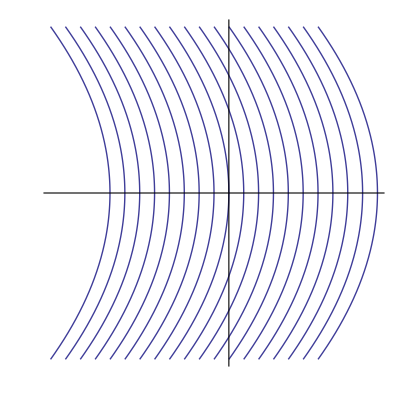

```mathematica
ParametricPlot[Table[{a-1/2y^2,y},{a,-1,1.25,0.125}],{y,-1,1},Ticks->None,AspectRatio->1]
```

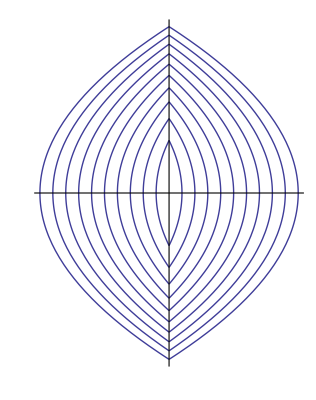

```mathematica
ParametricPlot[Join[Table[{-a+a z^2,Sqrt[2a]z},{a,0.125,1.25,0.125}],Table[{a-a z^2,Sqrt[2a]z},{a,0.125,1.25,0.125}]],{z,-1,1},Ticks->None]
```

```mathematica
?NDSolve
```

NDSolve[eqns,y,{x,x_min,x_max}] finds a numerical solution to the ordinary differential equations eqns for the function y with the independent variable x in the range x_min to x_max. 
NDSolve[eqns,y,{x,x_min,x_max},{t,t_min,t_max}] finds a numerical solution to the partial differential equations eqns. 
NDSolve[eqns,{y_1,y_2,…},{x,x_min,x_max}] finds numerical solutions for the functions y_i.

```mathematica
s=NDSolve[{x'[t]==y[t],y'[t]==If[x[t]+0.3y[t]>0,-1,1],x[0]==0,y[0]==1},{x,y},{t,20},MaxSteps->10000]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 2.63211.

{{x→InterpolatingFunction[{{0.,2.63211}},<>],y→InterpolatingFunction[{{0.,2.63211}},<>]}}

```mathematica
s=NDSolve[{x'[t]==y[t],y'[t]==-Sign[x[t]+0.04y[t]],x[0]==0,y[0]==1},{x,y},{t,20},MaxSteps->10000]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 13.5.

{{x→InterpolatingFunction[{{0.,13.5}},<>],y→InterpolatingFunction[{{0.,13.5}},<>]}}

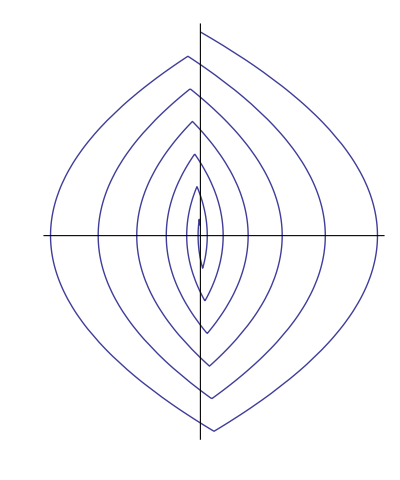

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,13.45},AspectRatio->1.2,Ticks->None]
```